```mathematica
prog:=(ergPairs={};
Module[{file,i,line,toNum,nums,nums2,event,nps,erg0,erg1},
file=OpenRead["c:\\git\\fusor-stuff\\mcnp\\np03.1p"];
toNum=Interpreter[Number];
i=0;
ReadLine[file];ReadLine[file];ReadLine[file];
While[(line=ReadLine[file])=!=EndOfFile,
nums=toNum[StringSplit[line]];
If[Length[nums]==2&&nums[[2]]==1000,
nps=nums[[1]];Print[nps];
nums=toNum[StringSplit[ReadLine[file]]];
nums2=toNum[StringSplit[ReadLine[file]]];
event=nums[[1]];
erg0=nums2[[7]];
While[event==4000,
nums=toNum[StringSplit[ReadLine[file]]];
nums2=toNum[StringSplit[ReadLine[file]]];
event=nums[[1]];
erg1=nums2[[7]];
If[event==4000,AppendTo[ergPairs,{erg0,erg1}];];
erg0=erg1;
];
];
i++;
];
Close[file];
Print[i];
])
```

```mathematica
prog
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

135

```mathematica
ergPairs
```

{{2.53×10^-8,2.684×10^-8},{2.684×10^-8,2.3662×10^-8},{2.3662×10^-8,8.8644×10^-9},{8.8644×10^-9,3.4693×10^-8},9862,{1.6615×10^-8,3.1406×10^-9},{3.1406×10^-9,6.9583×10^-8},{6.9583×10^-8,2.6425×10^-9}}
 |  |  |  |

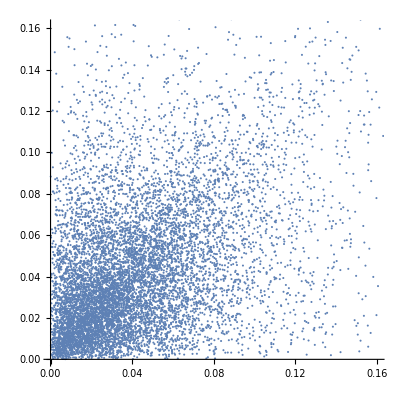

```mathematica
ListPlot[10^6 ergPairs,AspectRatio->1]
```

```mathematica
Correlation[ergPairs]
```

{{1.,0.453092},{0.453092,1.}}

```mathematica
Correlation[ergPairs]
```

{{1.,0.457891},{0.457891,1.}}